(g1 (-e1+v))/(1+835983. ⅇ^(0.181818 v))

(g2 (-e2+v))/((1+ⅇ^(16+v/5)) (1+0.000887567 ⅇ^(-0.135135 v))^2)

(g3 (-e3+v))/((1+ⅇ^(1/17 (-10-v))) (1+237.864 ⅇ^(0.0943396 v)))

(g4 (-e4+v))/((1+ⅇ^(13+v/6)) (1+0.000859789 ⅇ^(-0.117647 v))^4)

(g5 (-e5+v) If[InterpolatingFunction[{{-120.,-32.2524}},<>][v]<500,CaiFn[v]/50000,0.01])/(0.001+If[InterpolatingFunction[{{-120.,-32.2524}},<>][v]<500,CaiFn[v]/50000,0.01])

(1. g6 (-e6+v))/((1.+0.0955767 ⅇ^(-0.0869565 v))^4)

(9.92919 ⅇ^(v/11) g7 (-1. e7+v) If[0.004 InterpolatingFunction[{{-120.,-32.2524}},<>][v]<1,0.004 CaiFn[v],1])/(4.-9.92919 ⅇ^(v/11))

(11.9039 ⅇ^(23 v/90) g8 (-1. e8+v))/(0.01+0.545982 ⅇ^(v/5)+11.9039 ⅇ^(23 v/90))

(g9 (-e9+v))/((1+0.0287246 ⅇ^(-v/10))^3 (1+6011.88 ⅇ^(0.149254 v)))

(g10 (-e10+v))/((1+0.0287246 ⅇ^(-v/10))^3)

g11 (-e11+v)

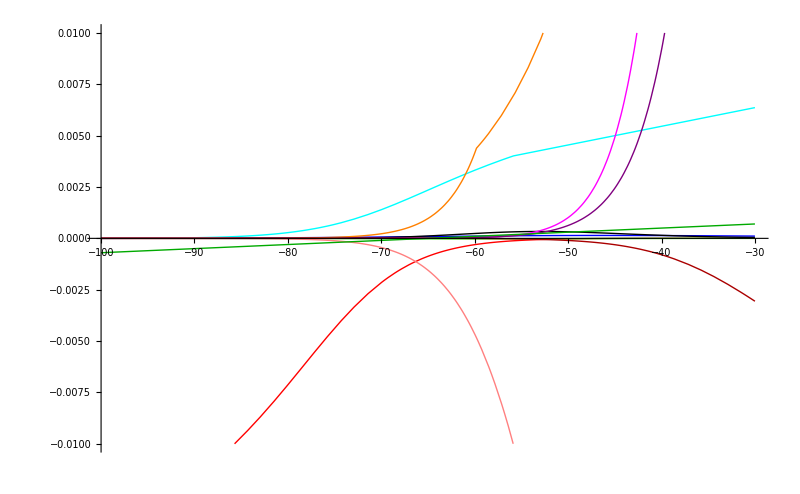

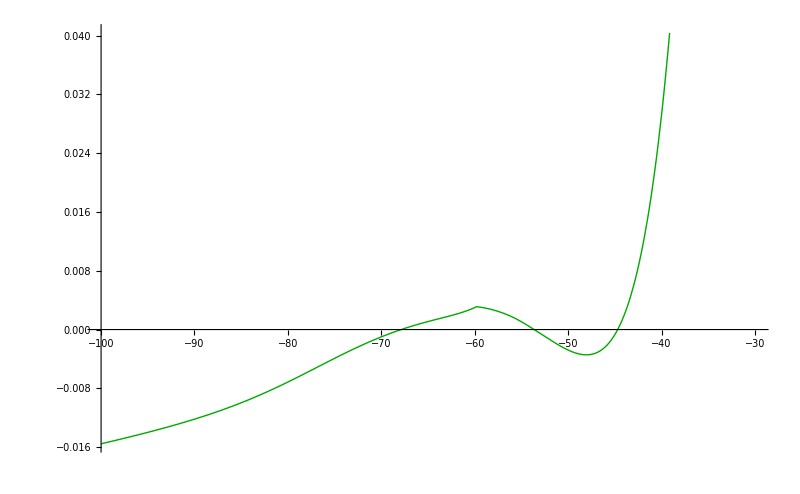

{-0.0210996,-0.0205574,-0.0200142,-0.0194697,-0.0189235,-0.0183747,-0.0178225,-0.0172654,-0.0167016,-0.0161285,-0.0155426,-0.0149392,-0.0143121,-0.013653,-0.0129516,-0.0121952,-0.0113694,-0.0104594,-0.00945299,-0.00834478,-0.00714182,-0.005868,-0.00456433,-0.00328322,-0.00207788,-0.00099166,-0.000050764,0.00074184,0.00141903,0.00208603,0.00299191,0.00266176,0.00173134,0.000295922,-0.00133589,-0.0027862,-0.00343737,-0.00233134,0.00195434,0.0114782}

(g1 (-Ear+v))/(1+835983. ⅇ^(0.181818 v))+(g2 (-Ecat+v))/((1+ⅇ^(16+v/5)) (1+0.000887567 ⅇ^(-0.135135 v))^2)+(g3 (-Ek+v))/((1+ⅇ^(1/17 (-10-v))) (1+237.864 ⅇ^(0.0943396 v)))+(g4 (-Ek+v))/((1+ⅇ^(13+v/6)) (1+0.000859789 ⅇ^(-0.117647 v))^4)+(1. g6 (-Ek+v))/((1.+0.0955767 ⅇ^(-0.0869565 v))^4)+(11.9039 ⅇ^(23 v/90) g8 (-1. Ek+v))/(0.01+0.545982 ⅇ^(v/5)+11.9039 ⅇ^(23 v/90))+(g10 (-Ena+v))/((1+0.0287246 ⅇ^(-v/10))^3)+(g9 (-Ena+v))/((1+0.0287246 ⅇ^(-v/10))^3 (1+6011.88 ⅇ^(0.149254 v)))+g11 (-Epas+v)+(9.92919 ⅇ^(v/11) g7 (-1. Ek+v) If[0.004 InterpolatingFunction[{{-120.,-32.2524}},<>][v]<1,0.004 CaiFn[v],1])/(4.-9.92919 ⅇ^(v/11))+(g5 (-Ek+v) If[InterpolatingFunction[{{-120.,-32.2524}},<>][v]<500,CaiFn[v]/50000,0.01])/(0.001+If[InterpolatingFunction[{{-120.,-32.2524}},<>][v]<500,CaiFn[v]/50000,0.01])

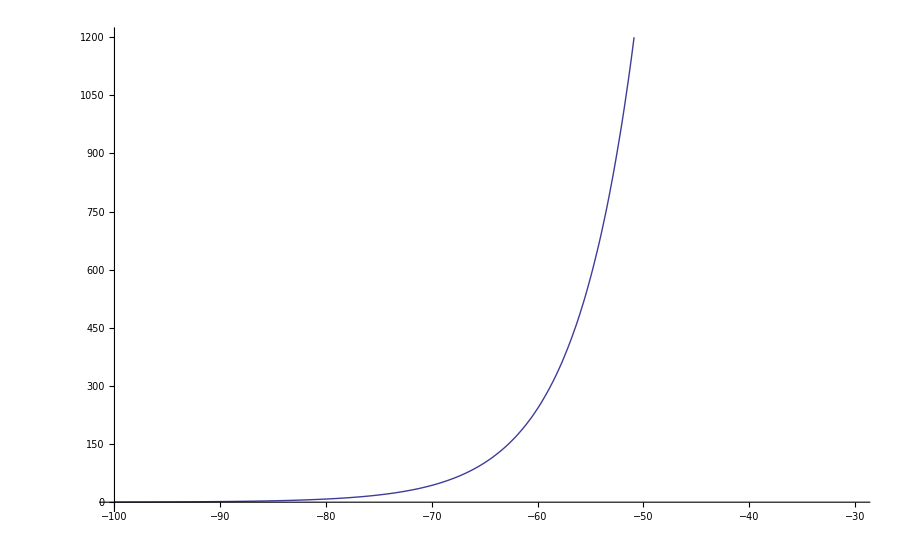

```mathematica
(* test interpolation for calcium *)
VforCa={{-120},{-117.75},{-115.5},{-113.25},{-111},{-108.75},{-106.5},{-104.25},{-102},{-99.7499},{-97.4999},{-95.2499},{-92.9999},{-90.7499},{-88.5},{-86.25},{-84},{-81.75},{-79.5},{-77.25},{-75},{-72.75},{-70.5},{-68.25},{-66},{-63.75},{-61.5},{-59.2501},{-57.0001},{-54.75},{-52.5},{-50.25},{-48},{-45.75},{-43.5},{-41.2502},{-39.0004},{-36.7508},{-34.5014},{-32.2524}};
CaiCa={{0.0529312},{0.0582999},{0.0659793},{0.0769738},{0.0927292},{0.115329},{0.147777},{0.194415},{0.26152},{0.358182},{0.497582},{0.698863},{0.989865},{1.41115},{2.02188},{2.90855},{4.19781},{6.07542},{8.8144},{12.8168},{18.676},{27.2692},{39.8963},{58.4875},{85.9151},{126.461},{186.524},{275.679},{408.277},{605.856},{900.759},{1341.55},{2001.07},{2988.34},{4465.84},{6674.13},{9965.85},{14850.5},{22049},{32551.5}};
CaiPairs=Transpose[{Flatten[VforCa],Flatten[CaiCa]}];
CaiFn=Interpolation[CaiPairs];
(* Plot[{CaiFn[v]},{v,-100,-30},PlotRange->{0,1200}] *)
(* iARfp + iCATAp + iK2p + 
iKAp + iKAHPSp + iKDRFSp +
iKCFASTp + iKMp + iNAF2p + iNAPFp + iPASp *)
Clear[iARf, iCATAf, iK2f, iKAf, iKAHPSf,iKDRFSf,iKCFASTf,iKMf,iNAF2f,iNAPFf, iPASf];
Clear[iARp, iCATAp, iK2p, iKAp, iKAHPSp,iKDRFSp,iKCFASTp,iKMp,iNAF2p,iNAPFp, iPASp];
Clear[x,y,z,v,i,e]
Clear[allCURf]
myColorList:={Red,Green,Blue, Black, Cyan, Magenta, Orange, Purple, Pink, Darker[Red],Darker[Green]};
Needs["PlotLegends`"]
(* CAL V->Ica // unused *)
gbarCAL=0.0005;
alphaCAL=1.6/(1+Exp[-0.072*(v-5)]);
betaCAL=0.02*(v+8.9)/(Exp[(v+8.9)/5]-1);
minfCAL=alphaCAL/(alphaCAL+betaCAL);
icaCALf=gbarCAL*minfCAL^2*(v-12);
(* CAD Ica->cai // unused *)
betaCAD=0.02;
phiCAD=260000;
icaCAD=icaCALf;
caiCADf=Max[-phiCAD*icaCAD/betaCAD,0];
(* AR *)
gbarAR =2.5*10^-4 ;
eAR=-40 ;
minfAR =1/(1+Exp[(v+75)/5.5]) ;
gbarARion=gbarAR*minfAR;
iARf=gbarARion*(v-eAR);
iARfgplus= g*minfAR*(v-eAR); (* used for 3d *)
iARfeplus= gbarARion*(v-e);
iARp=Simplify[
g1*minfAR*(v-e1)
]
(* CATA *)
minfCATA=1/(1+Exp[(-v-52)/7.4]) ;
hinfCATA=1/(1+Exp[(v+80)/5]) ;
gbarCATA = 0.0001;
gbarCATAion = gbarCATA*minfCATA^2*hinfCATA;
iCATAf=gbarCATAion*(v-125);
iCATAp=Simplify[
g2*minfCATA^2*hinfCATA*(v-e2)
]
(* Plot[{iARf,iCATAf},{v,-100,-30},PlotStyle->myColorList,
PlotRangeClipping->False,PlotLegend->{"i-AR","i-CATA"},
LegendShadow->{-0.01,-0.01}, ImageSize->{800,600}] *)
(* K2 *)
eK2 = -100 ;
gbarK2 = 0.0001;
minfK2=1/(1+Exp[(-v-10)/17]) ;
hinfK2=1/(1+Exp[(v+58)/10.6]) ;
gbarK2ion = gbarK2*minfK2*hinfK2;
iK2f=gbarK2ion*(v-eK2);
iK2p=Simplify[
g3*minfK2*hinfK2*(v-e3)
]
(* KA *)
eKA = -100;
gbarKA = 0.002;
minfKA=1/(1+Exp[(-v-60)/8.5]) ;
hinfKA=1/(1+Exp[(v+78)/6]) ;
gbarKAion=gbarKA*minfKA^4*hinfKA;
iKAf=gbarKAion*(v-eKA);
iKAp=Simplify[
g4*minfKA^4*hinfKA*(v-e4)
]
(* Plot[{iK2f,iKAf},{v,-100,-30},PlotStyle->myColorList,
PlotRangeClipping->False,PlotLegend->{"i-K2","i-KA"},
LegendShadow->{-0.01,-0.01}, ImageSize->{800,600}] *)
(* KAHPSlow *)
caiKAHPS=CaiFn[v];
(* orig 62 but actually caiKAHPS = caiCADf; but problematic *)
alphaKAHPS=If[caiKAHPS<500,CaiFn[v]/50000,0.01];
gbarKAHPS=0.0001;
eKAHPS =-100;
minfKAHPS=alphaKAHPS/(alphaKAHPS+0.001);
gbarKAHPSion=gbarKAHPS*minfKAHPS;
iKAHPSf=gbarKAHPSion*(v-eKAHPS);
iKAHPSp=Simplify[
g5*minfKAHPS*(v-e5)
]
(* KDRFS *)
minfKDRFS=1.0/(1.0+Exp[(-v-27.0)/11.5]);
eKDRFS=-100 ;
gbarKDRFS = 0.1;
gbarKDRFSion=gbarKDRFS*minfKDRFS^4;
iKDRFSf=gbarKDRFSion*(v-eKDRFS);
iKDRFSp=Simplify[
g6*minfKDRFS^4*(v-e6)
]
(* Plot[{iKAHPSf,iKDRFSf},{v,-100,-30},PlotStyle->myColorList,
PlotRangeClipping->False,PlotLegend->{"i-KAHPS","i-KDRFS"},
LegendShadow->{-0.01,-0.01}, ImageSize->{800,600}] *)
(* KCFAST *)
(* solved with minf = alpha/(alpha+beta) WATCH OUT DEP ON cai! *)
eKCFAST=-100;
alphaKCFAST=If [v≤-10.0,2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27]),2*Exp[(-v-53.5)/27]];
betaKCFAST= If [v≤-10.0,2* (2*Exp[(-v-53.5)/27]-alphaKCFAST ),0];
(* minfKCFAST = alphaKCFAST/(alphaKCFAST+betaKCFAST); *)
minfKCFAST=If[v≤ -10.0,(2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27]))/(-2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27])+2* 2*Exp[(-v-53.5)/27]),1.0];
gbarKCFAST =0.01;
(* orig 62 but actual caiKCFAST=caiCADf; but problematic *)
caiKCFAST=CaiFn[v];
(* gbarKCFASTion=If[0.004*caiKCFAST<1,gbarKCFAST*minfKCFAST*0.004*caiKCFAST,gbarKCFAST*minfKCFAST]; *)
gbarKCFASTion=If[0.004*CaiFn[v]<1,gbarKCFAST*If[v≤ -10.0,(2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27]))/(-2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27])+2* 2*Exp[(-v-53.5)/27]),1.0]*0.004*CaiFn[v],gbarKCFAST*If[v≤ -10.0,(2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27]))/(-2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27])+2* 2*Exp[(-v-53.5)/27]),1.0]];
iKCFASTf=gbarKCFASTion*(v-eKCFAST);
iKCFASTp=Simplify[ 
g7*If[0.004*CaiFn[v]<1,0.004*CaiFn[v],1]*(2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27]))/
(-2*2/37.95*(Exp[(v+50)/11-(v+53.5)/27])+2* 2*Exp[(-v-53.5)/27])*(v-e7) 
]
(* KM *)
(* solved with minf = alpha/(alpha+beta) *)
gbarKM=3.75*10^-03;
alphaKM=0.02/(1+Exp[(-v-20)/5]);
betaKM=0.01*Exp[(-v-43)/18];
minfKM=alphaKM/(alphaKM+betaKM);
eKM=-100;
gbarKMion=gbarKM*minfKM;
iKMf=gbarKMion*(v-eKM);
iKMp=Simplify[
g8*minfKM*(v-e8)
]
(* Plot[{iKCFASTf,iKMf},{v,-100,-30},PlotStyle->myColorList,
PlotRangeClipping->False,PlotLegend->{"i-KCFAST","i-KM"},
LegendShadow->{-0.01,-0.01}, ImageSize->{800,600}] *)
(* NAF2 *)
fastNashiftNAF2=-2.5;
minfNAF2=1/(1+Exp[(-(v+fastNashiftNAF2)-38)/10]);
hinfNAF2=1/(1+Exp[((v+fastNashiftNAF2*0)+58.3)/6.7]);
eNAF2=50;
gbarNAF2 =0.150;
gbarNAF2ion =gbarNAF2*minfNAF2^3*hinfNAF2;
iNAF2f=gbarNAF2ion*(v-eNAF2); 
iNAF2p=Simplify[
g9*minfNAF2^3*hinfNAF2*(v-e9)
]
(* NAPF *)
fastNAPF = -2.5;
gbarNAPF =1.5*10^-4;
eNAPF=50;
minfNAPF=1/(1+Exp[(-(v+fastNAPF)-38)/10]);
gbarNAPFion=gbarNAPF*minfNAPF^3;
iNAPFf=gbarNAPFion*(v-eNAPF);
iNAPFp=Simplify[
g10*minfNAPF^3*(v-e10)
]
(* PAS *)
gbarPAS=2.0*10^-5;
ePAS=-65;
iPASf=gbarPAS*(v-ePAS);
iPASp=Simplify[
g11*(v-e11)
]
(* Plot[{iNAF2f,iNAPFf,iPASf},{v,-100,-30},PlotStyle->myColorList,
PlotRangeClipping->False,PlotLegend->{"i-NAF2","i-NAPF","i-PAS"},
LegendShadow->{-0.01,-0.01}, ImageSize->{800,600}] *)
Plot[{iARf,iCATAf,iK2f,iKAf,iKAHPSf,iKDRFSf,iKCFASTf,iKMf,iNAF2f,iNAPFf,iPASf},{v,-100,-30},
PlotRange->{-0.01,0.01},
PlotStyle->myColorList,
PlotRangeClipping->False,PlotLegend->{"i-AR","i-CATA","i-K2","i-KA","i-KAHPS","i-KDRFS","i-KCFAST","i-KM","i-NAF2","i-NAPF","iPAS"},
LegendShadow->{-0.01,-0.01}, ImageSize->{800,600}]
allCURf =iARf+iCATAf+iK2f+iKAf+iKAHPSf+iKDRFSf+ iKCFASTf+iKMf+ iNAF2f+iNAPFf+iPASf;
Plot[{allCURf},{v,-100,-30},
PlotStyle->myColorList,
PlotRangeClipping->True,
PlotLegend->{"All i"},
LegendShadow->{-0.01,-0.01}, ImageSize->{800,600}]
(* Mapping values through the function *)
allCURfx[vx_] :=allCURf/. v->vx;
Vonlysomacut={{-120},{-118},{-116},{-114},{-112},{-110},{-108},{-106},{-104},{-102},{-100},{-98},{-96},{-94},{-92},{-90},{-88},{-86},{-84},{-82},{-80},{-78},{-76},{-74},{-72},{-70},{-68},{-66},{-64},{-62},{-60},{-58},{-56},{-54},{-52},{-50},{-48},{-46},{-44},{-42}};
Map[allCURfx, Flatten[Vonlysomacut]]
allCURp=iARp+iCATAp+iK2p+iKAp+iKAHPSp+iKDRFSp+ iKCFASTp+iKMp+ iNAF2p+iNAPFp+iPASp;
allCURp /.{e1->Ear,e2->Ecat,e3->Ek,e4->Ek,e5->Ek,e6->Ek,e7->Ek,e8->Ek,e9->Ena,e10->Ena,e11->Epas}
```

```mathematica
CaiFn[-60]
```

241.845

```mathematica
1/0.004
```

250.